# In this file we turn on the dimple wire current

{x→3.2653×10^-14,y→1.70513×10^-14,z→0.000151911}

{109.3,106.381,24.8997}

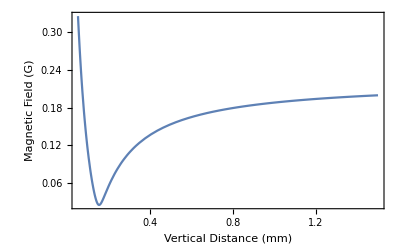
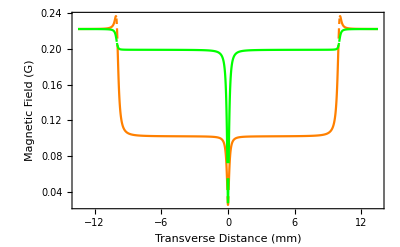
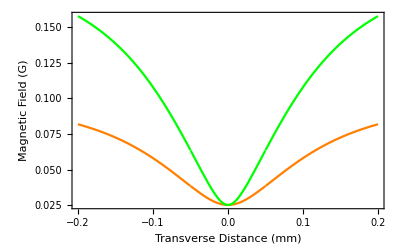

-Graphics3D-

```mathematica
μm=10^-6;
k=10^-7;
mA=mm=10^-3;
μ0=4π 10^-7;

(* Function FatXwire calculates the magnetic field at position (x0,y0,z0) of a rectangular conductor with finite width 2*hw.  We assume: (1) Current flows in the x direction from x1 -> x2; (2) The conductor is centered at y=yc and has width 2*hw; (3) The conductor lies entirely in the x-y plane (i.e. z=0). *)
FatXwire[x0_,y0_,z0_,hw_,yc_,x1_,x2_]:=Module[{dx1,dx2,dyPlus,dyMinus},
dx1=-x0+x1;
dx2=-x0+x2;
dyPlus=hw-y0+yc;
dyMinus=hw+y0-yc;
Return[10^-3/(2hw){0,ArcTan[(dx1 dyMinus)/(z0 √(dx1^2+dyMinus^2+z0^2))]-ArcTan[(dx2 dyMinus)/(z0 √(dx2^2+dyMinus^2+z0^2))]+ArcTan[(dx1 dyPlus)/(z0 √(dx1^2+dyPlus^2+z0^2))]-ArcTan[(dx2 dyPlus)/(z0 √(dx2^2+dyPlus^2+z0^2))],Log[(dx1+√(dx1^2+dyMinus^2+z0^2))/(dx2+√(dx2^2+dyMinus^2+z0^2))(dx2+√(dx2^2+dyPlus^2+z0^2))/(dx1+√(dx1^2+dyPlus^2+z0^2))]}];
];

(* Function FatYwire calculates the B-field at position (x0,y0,z0) for a conductor of width 2*hw at position x=xc running a finite length in y from y1->y2. We assume the conductor lies in the plane z=0. *)
FatYwire[x0_,y0_,z0_,hw_,xc_,y1_,y2_]:=Module[{dxPlus,dxMinus,dy1,dy2},
dxPlus=hw+x0-xc;
dxMinus=hw-x0+xc;
dy1=y0-y1;
dy2=-y0+y2;
Return[10^-3/(2 hw){ArcTan[(dxPlus dy1)/(z0 √(dxPlus^2+dy1^2+z0^2))]+ArcTan[(dxMinus dy1)/(z0 √(dxMinus^2+dy1^2+z0^2))]+ArcTan[(dxPlus dy2)/(z0 √(dxPlus^2+dy2^2+z0^2))]+ArcTan[(dxMinus dy2)/(z0 √(dxMinus^2+dy2^2+z0^2))],0,Log[(-dy1+√(dxPlus^2+dy1^2+z0^2))/(-dy1+√(dxMinus^2+dy1^2+z0^2))(dy2+√(dxMinus^2+dy2^2+z0^2))/(dy2+√(dxPlus^2+dy2^2+z0^2))]}];
];
(* Pick a coordinate system: "x" is the direction of the main chip wire, and "y" is the direction current flows along the dimple. *)
ChipTrapField[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=Module[{VecField},
VecField=Ix*FatXwire[x,y,z,50μm,0,-10mm,+10mm] (* main section of Z wire *)
+Ix*FatYwire[x,y,z,50μm,-10mm,-10mm,0mm] (* first leg of Z wire *)
+Ix*FatYwire[x,y,z,50μm,10mm,0mm,10mm] (* second leg of Z wire *)
+Iy*FatYwire[x,y,z,50μm,0,-10mm,10mm]+{Bx,By,0}; (* dimple wire *)
Return[Sqrt[VecField.VecField]]
]

z0[Ix_,Iy_,Bx_,By_]:=NMinimize[{ChipTrapField[x,y,z,Ix,Iy,Bx,By],-0.5mm<x<0.5mm,-0.5mm<y<0.5mm,2000μm>z>3μm},{x,y,z}][[2]]

μB =9.27*10^-24; (* J/T *)
mRb = 1.443*10^-25; (* kg *)
Dxx[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=D[10^-4 ChipTrapField[x,y,z,Ix,Iy,Bx,By],{x,2}];
Dxy[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=D[10^-4 ChipTrapField[x,y,z,Ix,Iy,Bx,By],x,y];
Dxz[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=D[10^-4 ChipTrapField[x,y,z,Ix,Iy,Bx,By],x,z];
Dyy[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=D[10^-4 ChipTrapField[x,y,z,Ix,Iy,Bx,By],{y,2}];
Dyz[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=D[10^-4 ChipTrapField[x,y,z,Ix,Iy,Bx,By],y,z];
Dzz[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=D[10^-4 ChipTrapField[x,y,z,Ix,Iy,Bx,By],{z,2}];
DMatrix[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=({{Dxx[x,y,z,Ix,Iy,Bx,By], Dxy[x,y,z,Ix,Iy,Bx,By], Dxz[x,y,z,Ix,Iy,Bx,By]}, {Dxy[x,y,z,Ix,Iy,Bx,By], Dyy[x,y,z,Ix,Iy,Bx,By], Dyz[x,y,z,Ix,Iy,Bx,By]}, {Dxz[x,y,z,Ix,Iy,Bx,By], Dyz[x,y,z,Ix,Iy,Bx,By], Dzz[x,y,z,Ix,Iy,Bx,By]}});

(* The funciton ChipTrapFrequencies calculates the position z0 where the trap is centered. It does this using the values for the chip currents and bias fields. It assumes the trap is centered at x=0 and y=0 *)
ChipTrapFrequencies[Ix_,Iy_,Bx_,By_]:= Module[{x,y,z,DMatrixDiag,xmin,ymin,zmin},
{xmin,ymin,zmin}=z0[Ix,Iy,Bx,By];
xmin=xmin[[2]];
ymin=ymin[[2]];
zmin=zmin[[2]];
DMatrixDiag=Eigensystem[DMatrix[x,y,z,Ix,Iy,Bx,By]/.{x->xmin,y->ymin,z->zmin}];
Return[
 Sqrt[μB Abs[DMatrixDiag[[1]]]/mRb]/(2π) (* in Hz *)
]
]

A=.005; (* Scaling factor for the chip currents *)
CLg1=-3.250*A; (* main Z-wire current; flows in x direction in these coordinates, z direction in cart coordinates *)
CLd1=1.23*A*1;(* dimple wire current; flows in y direction in these coordinates, x direction in cart coordinates *)
Bx1=-0.90*22.6*1*A;  (* Bias field in x direction (these coordinates) or z direction (cart coordinates *)
By1=-1.75*22.6*1*A; (* Bias field in y direction (these coordinates) or x direction (cart coordinates *)
{x1,y1,z1}=z0[CLg1,CLd1,Bx1,By1]
x1=x1[[2]];
y1=y1[[2]];
z1=z1[[2]];

Bmin1=ChipTrapField[x1,y1,z1,CLg1,CLd1,Bx1,By1];
Depth1=ChipTrapField[x1,y1,1,CLg1,CLd1,Bx1,By1]-Bmin1;
freqs1=ChipTrapFrequencies[CLg1,CLd1,Bx1,By1]
(*GeometricMean[freqs1]*)

Plot1=Plot[ChipTrapField[x1,y1,z mm,CLg1,CLd1,Bx1,By1],{z,0.05,1.5},
Frame->True,Axes->False,
FrameLabel->{"Vertical Distance (mm)","Magnetic Field (G)"},
LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Background->None],
Background->White,
ImageSize->400
];
Plot2=Plot[{ChipTrapField[x mm,y1,z1,CLg1,CLd1,Bx1,By1],ChipTrapField[x1,x mm,z1,CLg1,CLd1,Bx1,By1]},{x,-13.5,13.5},PlotStyle->{Orange,Green},
Frame->True,Axes->False,
FrameLabel->{"Transverse Distance (mm)","Magnetic Field (G)"},
LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Background->None],
Background->White,
ImageSize->400
];
Plot3=Plot[{ChipTrapField[x mm,y1,z1,CLg1,CLd1,Bx1,By1],ChipTrapField[x1,x mm,z1,CLg1,CLd1,Bx1,By1]},{x,-.2,.2},PlotStyle->{Orange,Green},
Frame->True,Axes->False,
FrameLabel->{"Transverse Distance (mm)","Magnetic Field (G)"},
LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Background->None],
Background->White,
ImageSize->400
];
{Plot1, Plot2, Plot3}
Ldist=.2;
dplot3d=Plot3D[ChipTrapField[x mm,y mm,z1,CLg1,CLd1,Bx1,By1],{x,-Ldist,Ldist},{y,-Ldist,Ldist},AxesLabel->{"x (mm)", "y (mm)","B(G)     "},LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->14,Background->None],PlotLabel->"Magnetic field of the initial trap",PlotTheme->"Web",ImageSize->500,PlotPoints->50]
```

```mathematica
<<PhysicalConstants`
t=.;
Kilogram=Meter=Joule =Second=Kelvin=1;
T = 20*10^-9; (* Temperature in K *)
fc = 0.5; (* fraction of condensed atoms *)

m =87*ProtonMass;
a=104.5*BohrRadius; (* scattering length *)
hbar=PlanckConstantReduced;
kb = BoltzmannConstant;

ω=2π*freqs1; (* Trap frequencies *)
ωbar=(∏_(i=1)^3 ω[[i]])^(1/3);
Na = ((kb*T)/(0.94*hbar*ωbar))^3/(1-fc) (* Number of atoms in the trap *)
σ=√((kb*T)/(m*ω^2))

(* delta-kick cooling*)
dkkt=0.1; (* moment of the delta kick in sec*)
dkkd = 0.002;(* 1/2 duration of the delta kick in sec *)

A=.00003(*.000165*); (* Scaling factor for the chip currents *)(* 0.0012 for nonzero CLd1 *)
CLg1=-3.250*A; 
CLd1=1.23*A*1;
Bx1=-0.90*22.6*1*A;
By1=-1.75*22.6*1*A;
{x1,y1,z1}=z0[CLg1,CLd1,Bx1,By1]; x1=x1[[2]]; y1=y1[[2]]; z1=z1[[2]];
ωdkk=2π*ChipTrapFrequencies[CLg1,CLd1,Bx1,By1]

(*ωdkk=53.4*{1,1,1};*)

ωt[t_]:=ω*((1-UnitStep[t])+UnitStep[t-dkkt]-UnitStep[t-(dkkt+dkkd)]);
ωt[t_]:=ωdkk*(ⅇ^(-(t-dkkt)^2/(2 dkkd^2)));
N[(1/Sqrt[dkkd dkkt Sqrt[2π]])]
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

601.921

{2.00584×10^-6,2.06089×10^-6,8.8049×10^-6}

{53.1958,51.775,12.1185}

44.6622

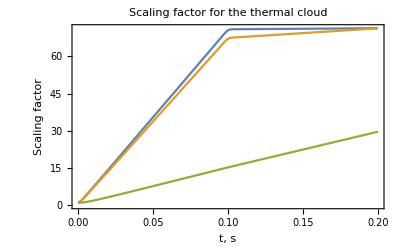
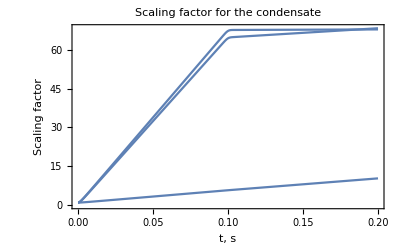
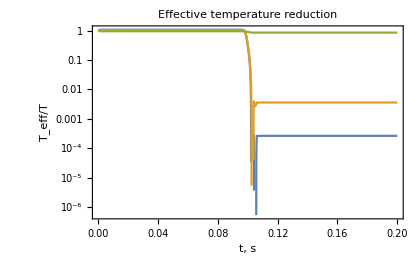

Final temperatures: {5.2429 pK,71.3437 pK,16953.9 pK}

```mathematica
(* Simulating the thermal component *)
nAtoms=Floor[Na(1-fc)];
nAtoms=1000;

(* Time step and length of the simulation *)
tau = 0.2;
dt = tau/100;
Ninc=Floor[10dt/dkkd]; (* increase in precision for the moment of dkc *)

force[t_,r_]:=-m ωt[t]^2 r;
propagate[t_,atom_,delt_]:={atom[[1]]+delt*atom[[2]]+(force[t,atom[[1]]]/m)delt^2/2,atom[[2]]+(force[t,atom[[1]]]/m)delt};

atoms=Transpose[{Transpose[RandomReal[NormalDistribution[0,#],nAtoms]&/@σ],RandomReal[NormalDistribution[0,Sqrt[kb*T/m]],{nAtoms,3}]}];
sigmas=Table[σ,{i,1,Floor[tau/dt+1]}];
Teff=Table[T*{1,1,1},{i,1,Floor[tau/dt+1]}];
timeline=Table[i*dt,{i,0,Floor[tau/dt]}];

For[Nt=1,Nt<=tau/dt,Nt++,
(* Increasing precision when applying dkc *)
If[ Abs[(Nt-1)dt-dkkt]<dkkd*3,
Do[atoms=propagate[(Nt-1)dt+i*dt/Ninc,#,dt/Ninc]&/@atoms,{i,0,Ninc-1}],
atoms=propagate[(Nt-1)dt,#,dt]&/@atoms
];
(*atoms=propagate[(Nt-1)dt,#,dt]&/@atoms;*)
Parray=First/@atoms;
meanParray=Mean[Parray];
sigmas[[Nt+1]]=Sqrt[Sum[(Parray[[i]]-meanParray)^2,{i,1,Length[Parray]}]/Length[Parray]];
Parray=Part[#,2]&/@atoms;
meanParray=Mean[Parray];
Teff[[Nt+1]]=(Sum[(Parray[[i]]-meanParray)^2,{i,1,Length[Parray]}]/Length[Parray])*(m/kb);
];
λth=Table[Interpolation[Transpose[{timeline,(Part[#,i]&/@sigmas)/σ[[i]]}]],{i,1,3}];

(* Simulating the condensate *)

λ[t_]={Subscript[λ, 1][t],Subscript[λ, 2][t],Subscript[λ, 3][t]};
sol=NDSolve[{Table[λ''[t][[j]]==ω[[j]]^2/(λ[t][[1]]λ[t][[2]]λ[t][[3]]λ[t][[j]])-(ωt[t][[j]])^2 λ[t][[j]],{j,1,3}],
λ[0]=={1,1,1},λ'[0]=={0,0,0}},λ[t],{t,0,tau}];



TeffoT=Table[Interpolation[Transpose[{timeline,(Part[#,i]&/@Teff)/T}]],{i,1,3}];
λthplot=Plot[{λth[[1]][t],λth[[2]][t],λth[[3]][t]},{t,0,tau},FrameLabel->{"t, s", "Scaling factor"},Frame->True, PlotLabel->"Scaling factor for the thermal cloud",
LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Background->None],
Background->White,
ImageSize->400];

λcondplot=Plot[λ[t]/.sol,{t,0,tau},FrameLabel->{"t, s", "Scaling factor"},Frame->True, PlotLabel->"Scaling factor for the condensate",
LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Background->None],
Background->White,
ImageSize->400];

Tplot=LogPlot[{TeffoT[[1]][t],TeffoT[[2]][t],TeffoT[[3]][t]},{t,0,tau},FrameLabel->{"t, s", "T_eff/T"},Frame->True, PlotLabel->"Effective temperature reduction",
LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Background->None],
Background->White,
ImageSize->420];

{λthplot, λcondplot, Tplot}

Print["Final temperatures: ",Last[Teff]*10^12 "pK"]
```

The difference in the final temperatures is due to the difference in the radial frequencies of the initial trap and, hence, different expansion rates.

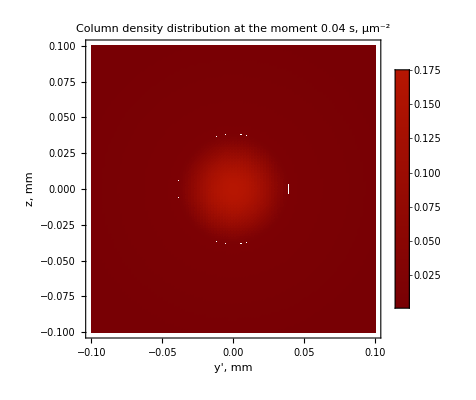

```mathematica
(* Density plot *)

R=1/ω √((hbar*ωbar)/m)(15 fc Na a √((m*ωbar)/hbar))^(1/5);
n2D[x_,y_]:=Na((1-fc)/(2π σ[[1]]σ[[2]])ⅇ^(-(x^2/(2 σ[[2]]^2)+y^2/(2 σ[[3]]^2)))+(5fc)/(2π R[[1]]R[[2]])Max[1-x^2/R[[1]]^2-y^2/R[[2]]^2,0]^(3/2))
n2Dt[x_,y_,t_]=(Na((1-fc)/(2π σ[[1]]σ[[2]]λth[[1]][t]λth[[2]][t])ⅇ^(-(x^2/(2 σ[[1]]^2(λth[[1]][t])^2)+y^2/(2 σ[[2]]^2(λth[[2]][t])^2)))+(5fc)/(2π R[[1]]R[[2]]Subscript[λ, 1][t]Subscript[λ, 2][t])Max[1-x^2/(R[[1]]^2(Subscript[λ, 1][t])^2)-y^2/(R[[2]]^2(Subscript[λ, 2][t])^2),0]^(3/2))/.sol)[[1]];

LPlot=100*10^-6/mm;
DensityPlot[n2Dt[x mm,y mm,0.04]/10^12,{x,-LPlot,LPlot},{y,-LPlot,LPlot},PlotLegends->Automatic,PlotLabel->"Column density distribution at\n the moment 0.04 s, μm^-2",PlotRange->{Automatic,Automatic,{0, 1}},PlotPoints->100,FrameLabel->{"y', mm","
z, mm"},ColorFunction->"SolarColors",ColorFunctionScaling->False,ImageSize->400]
```

```mathematica
LPlot=0.0005/mm;
{Animate[LogPlot[n2Dt[x mm,0,t]/10^12,{x,-LPlot,LPlot},PlotLegends->Automatic,PlotLabel->"Column density distribution, t="<>ToString[NumberForm[t,{3,3}]]<>" s",PerformanceGoal->"Quality", PlotRange->{{0,LPlot},{.0001,100}},Frame->True,Filling->None,FrameLabel->{"Radial distance, mm","Density, μm^-2"},
LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Background->None],
Background->White,
ImageSize->420],{t,0,tau,dt}],Animate[Plot[n2Dt[x mm,0,t]/10^12,{x,-LPlot,LPlot},PlotLegends->Automatic,PlotLabel->"Column density distribution, t="<>ToString[NumberForm[t,{3,3}]]<>" s",PerformanceGoal->"Quality", PlotRange->{{0,LPlot},{0,1}},Frame->True,Filling->None,FrameLabel->{"Radial distance, mm","Density, μm^-2"},
LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Background->None],
Background->White,
ImageSize->420],{t,0,tau,dt}]}
```

```mathematica
(* Export animation *)

LPlot=0.0005/mm;
Table[Export[NotebookDirectory[]<>"frames1/"<>ToString[NumberForm[t,{3,3}]]<>".png",LogPlot[n2Dt[x mm,0,t]/10^12,{x,-LPlot,LPlot},PlotLegends->Automatic,PlotLabel->"Column density distribution, t="<>ToString[NumberForm[t,{3,3}]]<>" s",PerformanceGoal->"Quality", PlotRange->{{0,LPlot},{.0001,100}},Frame->True,Filling->None,FrameLabel->{"Radial distance, mm","Density, μm^-2"},
LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Background->None],
Background->White,
ImageSize->420],ImageResolution->200],{t,0,tau,dt}];
```

```mathematica
Table[Export[NotebookDirectory[]<>"frames2/"<>ToString[NumberForm[t,{3,3}]]<>".png",Plot[n2Dt[x mm,0,t]/10^12,{x,-LPlot,LPlot},PlotLegends->Automatic,PlotLabel->"Column density distribution, t="<>ToString[NumberForm[t,{3,3}]]<>" s",PerformanceGoal->"Quality", PlotRange->{{0,LPlot},{0,1}},Frame->True,Filling->None,FrameLabel->{"Radial distance, mm","Density, μm^-2"},
LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Background->None],
Background->White,
ImageSize->420],ImageResolution->200],{t,0,tau,dt}];
```

```mathematica
LPlot=100*10^-6/mm;
Table[Export[NotebookDirectory[]<>"frames3/"<>ToString[NumberForm[t,{3,3}]]<>".png",DensityPlot[n2Dt[x mm,y mm,t]/10^12,{x,-LPlot,LPlot},{y,-LPlot,LPlot},PlotLegends->Automatic,PlotLabel->"Column density distribution, μm^-2, t="<>ToString[NumberForm[t,{3,3}]]<>" s",PlotRange->{Automatic,Automatic,{0, 1}},PlotPoints->100,FrameLabel->{"x, mm","
y, mm"},ColorFunction->"SolarColors",ColorFunctionScaling->False],ImageResolution->200],{t,0,tau,dt}];
```

```mathematica
Export[NotebookDirectory[]<>"Lthermal.png",λthplot,ImageResolution->300];
Export[NotebookDirectory[]<>"Lcondensate.png", λcondplot,ImageResolution->300];
Export[NotebookDirectory[]<>"Teff.png",Tplot,ImageResolution->300];
Export[NotebookDirectory[]<>"Bfield.png",dplot3d,ImageResolution->300];
```

```mathematica
(* Angle between the trap axes and the chip axes *)

DMatrix[x,y,z,CLg1,CLd1,Bx1,By1]/.x->x1/.y->y1/.z->z1//MatrixForm
vecs=Eigenvectors[%]
%//MatrixForm
ArcCos[vecs[[2]].{0,1,0}]*180/π
ArcCos[vecs[[3]].{1,0,0}]*180/π
```

(1454.75 | -2430.12 | 3.32047×10^-7
-2430.12 | 5880.9 | 7.31088×10^-7
3.32047×10^-7 | 7.31088×10^-7 | 7341.6)

{{-4.79544×10^-10,1.29831×10^-9,1.},{0.404155,-0.914691,1.38136×10^-9},{-0.914691,-0.404155,8.60837×10^-11}}

(-4.79544×10^-10 | 1.29831×10^-9 | 1.
0.404155 | -0.914691 | 1.38136×10^-9
-0.914691 | -0.404155 | 8.60837×10^-11)

156.162

156.162

```mathematica
({{xold}, {yold}})=({{-0.9146906078552439, -0.40415478705739066}, {+0.40415478705739055, -0.9146906078552437}}).({{x}, {y}})
xn[x_,y_]:=xnew;
yn[x_,y_]:=ynew;
```

{{-0.914691 x-0.404155 y},{0.404155 x-0.914691 y}}

```mathematica
(* BFieldRotated is in Tesla, not Gauss! *)
Ldist=0.0002;
BFieldRotated[x_,y_]:=10^-4 ChipTrapField[-0.9146906078552439 x-0.40415478705739066 y,-0.40415478705739055 x+0.9146906078552437 y,z1,CLg1,CLd1,Bx1,By1];
{Plot3D[BFieldRotated[x,y],{x,-Ldist,Ldist},{y,-Ldist,Ldist},AxesLabel->{x,y}],
Plot3D[10^-4 ChipTrapField[x,y,z1,CLg1,CLd1,Bx1,By1],{x,-Ldist,Ldist},{y,-Ldist,Ldist},AxesLabel->{x,y}]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
{109.30048178902186,106.38104898867913,24.89969413664885}
```

```mathematica
N[Sqrt[μB *D[BFieldRotated[x,y1],{x,2}]/mRb/.x->x1]/(2π) ]
 N[Sqrt[μB *D[BFieldRotated[x1,y],{y,2}]/mRb/.y->y1]/(2π) ]
angle=π+N[ArcSin[0.40415478705739066]]
180-%*180/π
Sin[angle]
Cos[angle]
```

3.42263

7.75234

3.55765

-23.8382

-0.404155

-0.914691

```mathematica
Ldist=10^(-4);
newChipTrap[x_,y_,z_]:=10^-4 ChipTrapField[-0.9146906078552439 z-0.40415478705739066 y,-0.40415478705739055 z+0.9146906078552437 y,z1+x,CLg1,CLd1,Bx1,By1];
Plot3D[newChipTrap[x,y,0],{x,-Ldist,Ldist},{y,-Ldist,Ldist},AxesLabel->{x,y}]
Plot3D[10^-4 ChipTrapField[x,y,z1,CLg1,CLd1,Bx1,By1],{x,-Ldist,Ldist},{y,-Ldist,Ldist},AxesLabel->{x,y}]
```

### Finding the most symmetric trap in the (x, y)-plane

```mathematica
DMatrix[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=({{Dxx[x,y,z,Ix,Iy,Bx,By], Dxy[x,y,z,Ix,Iy,Bx,By], 0}, {Dxy[x,y,z,Ix,Iy,Bx,By], Dyy[x,y,z,Ix,Iy,Bx,By], 0}, {0, 0, 0}});


asymmetry[Iz_,Id_]:=Module[{CLg1, CLd1,Bx1,By1,A,freqs1},
A=1; (* Scaling factor for the chip currents *)
CLg1=-Iz*A; (* main Z-wire current; flows in x direction in these coordinates, z direction in cart coordinates *)
CLd1=Id*A*1;(* dimple wire current; flows in y direction in these coordinates, x direction in cart coordinates *)
Bx1=-0.90*22.6*1*A;  (* Bias field in x direction (these coordinates) or z direction (cart coordinates *)
By1=-1.75*22.6*1*A; (* Bias field in y direction (these coordinates) or x direction (cart coordinates *)
freqs1=ChipTrapFrequencies[CLg1,CLd1,Bx1,By1];
Return[Abs[(freqs1[[1]]-freqs1[[2]])/(freqs1[[1]]+freqs1[[2]])]]
]
```

```mathematica
ParallelTable[asymmetry[x,y],{x,0,3.5},{y,0, 3.5}]
NMinimize[{asymmetry[xx,yy],0.5<xx<3,1<yy<3},{xx,yy}]
```

```mathematica
FindMinimum[asymmetry[xx,yy],{{xx,1},{yy,1}}]
```

```mathematica
dataa=Table[{xx,yy,asymmetry[xx,yy]},{xx,0.1,3.5,0.2},{yy,0.1,3.5,0.2}]
```

```mathematica
dataal=Flatten[dataa,1];
ListPlot3D[dataal]
```

-Graphics3D-

```mathematica
SortBy[dataal,Last]
```

```mathematica
dataa=Table[{xx,yy,asymmetry[xx,yy]},{xx,0.5,0.9,0.1},{yy,0.5,0.9,0.1}]
```

{{{0.5,0.5,0.969008},{0.5,0.6,0.866496},{0.5,0.7,0.757124},{0.5,0.8,0.876788},{0.5,0.9,0.982368}},{{0.6,0.5,0.389172},{0.6,0.6,0.211806},{0.6,0.7,0.282963},{0.6,0.8,0.571533},{0.6,0.9,0.699129}},{{0.7,0.5,0.351286},{0.7,0.6,0.15623},{0.7,0.7,0.0643166},{0.7,0.8,0.298239},{0.7,0.9,0.454016}},{{0.8,0.5,0.678892},{0.8,0.6,0.934487},{0.8,0.7,0.11334},{0.8,0.8,0.118474},{0.8,0.9,0.269187}},{{0.9,0.5,0.799958},{0.9,0.6,0.283316},{0.9,0.7,0.722371},{0.9,0.8,0.532886},{0.9,0.9,0.125581}}}

```mathematica
dataal=Flatten[dataa,1];
SortBy[dataal,Last]
```

{{0.7,0.7,0.0643166},{0.8,0.7,0.11334},{0.8,0.8,0.118474},{0.9,0.9,0.125581},{0.7,0.6,0.15623},{0.6,0.6,0.211806},{0.8,0.9,0.269187},{0.6,0.7,0.282963},{0.9,0.6,0.283316},{0.7,0.8,0.298239},{0.7,0.5,0.351286},{0.6,0.5,0.389172},{0.7,0.9,0.454016},{0.9,0.8,0.532886},{0.6,0.8,0.571533},{0.8,0.5,0.678892},{0.6,0.9,0.699129},{0.9,0.7,0.722371},{0.5,0.7,0.757124},{0.9,0.5,0.799958},{0.5,0.6,0.866496},{0.5,0.8,0.876788},{0.8,0.6,0.934487},{0.5,0.5,0.969008},{0.5,0.9,0.982368}}

```mathematica
dataa=Table[{xx,yy,asymmetry[xx,yy]},{xx,1.3,1.7,0.1},{yy,1.1,1.5,0.1}]
dataal=Flatten[dataa,1];
SortBy[dataal,Last]
```

{{{1.3,1.1,0.900019},{1.3,1.2,0.515079},{1.3,1.3,0.262148},{1.3,1.4,0.182283},{1.3,1.5,0.183409}},{{1.4,1.1,0.651594},{1.4,1.2,0.820579},{1.4,1.3,0.0640799},{1.4,1.4,0.702183},{1.4,1.5,0.14849}},{{1.5,1.1,0.654862},{1.5,1.2,0.706791},{1.5,1.3,0.0686113},{1.5,1.4,0.161407},{1.5,1.5,0.819701}},{{1.6,1.1,0.423649},{1.6,1.2,0.350602},{1.6,1.3,0.406964},{1.6,1.4,0.238411},{1.6,1.5,0.85176}},{{1.7,1.1,0.505366},{1.7,1.2,0.268167},{1.7,1.3,0.201023},{1.7,1.4,0.690202},{1.7,1.5,0.920994}}}

{{1.4,1.3,0.0640799},{1.5,1.3,0.0686113},{1.4,1.5,0.14849},{1.5,1.4,0.161407},{1.3,1.4,0.182283},{1.3,1.5,0.183409},{1.7,1.3,0.201023},{1.6,1.4,0.238411},{1.3,1.3,0.262148},{1.7,1.2,0.268167},{1.6,1.2,0.350602},{1.6,1.3,0.406964},{1.6,1.1,0.423649},{1.7,1.1,0.505366},{1.3,1.2,0.515079},{1.4,1.1,0.651594},{1.5,1.1,0.654862},{1.7,1.4,0.690202},{1.4,1.4,0.702183},{1.5,1.2,0.706791},{1.5,1.5,0.819701},{1.4,1.2,0.820579},{1.6,1.5,0.85176},{1.3,1.1,0.900019},{1.7,1.5,0.920994}}